```mathematica
data=Import["D:\\6 семестр\\Методы вычислений\\LR_2\\LR_2\\LR_2\\OUTPUT\\data.txt","Data"];
```

```mathematica
dataEx=Import["D:\\6 семестр\\Численные методы решения задач математической физики\\LR_2_new-master\\LR_2\\OUTPUT\\example3Ex.txt","Data"];
```

```mathematica
dataIm=Import["D:\\6 семестр\\Численные методы решения задач математической физики\\LR_2_new-master\\LR_2\\OUTPUT\\example3Im.txt","Data"];
```

```mathematica
dataMix=Import["D:\\6 семестр\\Численные методы решения задач математической физики\\LR_2_new-master\\LR_2\\OUTPUT\\example3Mix.txt","Data"];
```

```mathematica
data=data/Max[data];
```

```mathematica
BarLeg=BarLegend["TemperatureMap",Table[x,{x,0,1,0.001}]];
Manipulate[ArrayPlot[{data[[tau]]},ColorFunction->ColorData["TemperatureMap"],ColorFunctionScaling->False,PlotLegends->Placed[BarLeg,Below],PlotLabel->Style[τ==tau 0.01]],{tau,1,Length[data],5}]
```

Part::partd: Part specification data⟦9811⟧ is longer than depth of object.

ArrayPlot::mat: Argument {data⟦9811⟧} at position 1 is not a list of lists.

Part::partd: Part specification data⟦9811⟧ is longer than depth of object.

ArrayPlot::mat: Argument {data⟦9811⟧} at position 1 is not a list of lists.

Part::partd: Part specification data⟦9811⟧ is longer than depth of object.

ArrayPlot::mat: Argument {data⟦9811⟧} at position 1 is not a list of lists.

Part::partd: Part specification data⟦9811⟧ is longer than depth of object.

ArrayPlot::mat: Argument {data⟦9811⟧} at position 1 is not a list of lists.

Part::partd: Part specification data⟦9811⟧ is longer than depth of object.

ArrayPlot::mat: Argument {data⟦9811⟧} at position 1 is not a list of lists.

Part::partd: Part specification data⟦9811⟧ is longer than depth of object.

ArrayPlot::mat: Argument {data⟦9811⟧} at position 1 is not a list of lists.

Part::partd: Part specification data⟦9811⟧ is longer than depth of object.

ArrayPlot::mat: Argument {data⟦9811⟧} at position 1 is not a list of lists.

Part::partd: Part specification data⟦9811⟧ is longer than depth of object.

ArrayPlot::mat: Argument {data⟦9811⟧} at position 1 is not a list of lists.

Part::partd: Part specification data⟦9811⟧ is longer than depth of object.

ArrayPlot::mat: Argument {data⟦9811⟧} at position 1 is not a list of lists.

Part::partd: Part specification data⟦9811⟧ is longer than depth of object.

ArrayPlot::mat: Argument {data⟦9811⟧} at position 1 is not a list of lists.

Part::partd: Part specification data⟦9811⟧ is longer than depth of object.

ArrayPlot::mat: Argument {data⟦9811⟧} at position 1 is not a list of lists.

```mathematica
gif=Table[ArrayPlot[{data[[tau]]},ColorFunction->ColorData["TemperatureMap"],ColorFunctionScaling->False,PlotLegends->Placed[BarLeg,Below],PlotLabel->Style[τ==tau 0.01]],{tau,1,Length[data],1}];
```

```mathematica
Export["D:\\6 семестр\\Методы вычислений\\LR_2\\tempgif1.gif",gif]
```

D:\6 семестр\Методы вычислений\LR_2\tempgif1.gif

```mathematica
Пример 3
```

```mathematica
sigma=2;
cappa=0.5;
cc=5;
u[x_,t_]:=If[x>=cc t,0,(sigma (cc /cappa) (cc t-x))^(1/sigma)]
```

```mathematica
xcomp=Table[x,{x,0,9.8,0.2}];
```

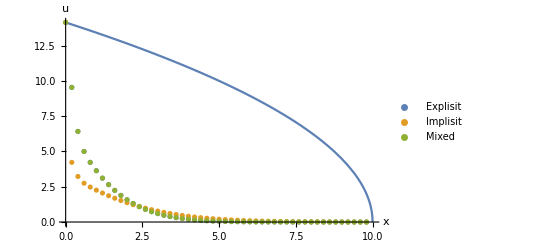

```mathematica
Show[Plot[(sigma cc/cappa (cc tt-xx))^(1/sigma),{xx,0,10},AxesLabel->{"x","u"}],ListPlot[{Transpose[{xcomp,dataEx[[-1]]}],Transpose[{xcomp,dataIm[[-1]]}],Transpose[{xcomp,dataMix[[-1]]}]},PlotRange->All,PlotLegends->{Explisit,Implisit,Mixed}]]
```

```mathematica
tt=1000 0.0002;
uu=Table[(sigma (cc /cappa) (cc tt-xx))^(1/sigma),{xx,0,10,0.2}];
```

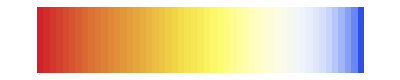

```mathematica
uu=uu/Max[uu];
ArrayPlot[{uu},ColorFunction->ColorData["TemperatureMap"],ColorFunctionScaling->False,PlotLegends->Placed[BarLeg,Below]]
```

```mathematica
Пример 0
```

```mathematica
u[x_,t_,lambda_]:=Sin[π x] Exp[- lambda t];
```

```mathematica
Manipulate[Plot[u[xx,tt,1],{xx,0,10},PlotRange->{{0,10},{-1,1}}],{tt,0,10}]
```

```mathematica
Manipulate[Plot[{u[xx,tt,0.5],u[xx,tt,1],u[xx,tt,2]},{xx,0,1},PlotRange->{{0,1},{-1,1}},PlotLegends->Automatic,AxesLabel->Automatic],{tt,0,10}]
```

```mathematica
data0Ex=Import["D:\\6 семестр\\Методы вычислений\\LR_2_new-master\\LR_2\\OUTPUT\\example0ExH2.txt","Data"];
```

```mathematica
Manipulate[ListLinePlot[data0Ex[[tt]],PlotRange->{{0,Length[data0Ex[[1]]]+1},{-1,1}},AxesLabel->{"x","u"},PlotLabel->tt*0.01],{tt,1,Length[data0Ex],1}]
```

Part::partd: Part specification data0Ex⟦1201⟧ is longer than depth of object.

Part::partd: Part specification data0Ex⟦1⟧ is longer than depth of object.

ListLinePlot::lpn: data0Ex⟦1201⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

```mathematica
data0Ex[[501]]
```

{0,0.0448645,0.0886243,0.130202,0.168573,0.202794,0.232021,0.255535,0.272757,0.283263,0.286794,0.283263,0.272757,0.255535,0.232021,0.202794,0.168573,0.130202,0.0886243,0.0448645,0}

```mathematica
uu=Table[u[xx,1,1],{xx,0,1,0.1}]
```

{0.,0.113681,0.216234,0.297621,0.349874,0.367879,0.349874,0.297621,0.216234,0.113681,4.50522×10^-17}

```mathematica
Norm[data0Ex[[-1]]-Table[u[xx,3,1],{xx,0,1,0.1/2}]]
```

0.000381943

```mathematica
0.000381943/0.00108951
```

0.350564

```mathematica
Log[2,%]
```

-1.51225

```mathematica
Отладка
```

```mathematica
1/0.2 1/2(1/π^2+1/π^2)//N
```

0.506606

```mathematica
1/0.1 %
```

1.01321

```mathematica
Sin[π 0.1]
```

0.309017

```mathematica
1/3//N
```

0.333333